10 a (1-x) x Cos[a x]+10 (1-x) Sin[a x]-10 x Sin[a x]

-20 (a x Cos[a x]+Sin[a x])+10 (1-x) (2 a Cos[a x]-a^2 x Sin[a x])

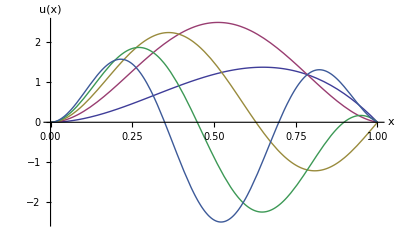

conv_diff_u.pdf

```mathematica
(** ODE: u u_x = u_xx + s
Exact solution: u = 10*x*(1-x)*sin(a*x)
**)
amin=1;
amax=10;
u[x_,a_]:=10*x*(1-x)*Sin[a*x]
ux=D[u[x,a],x]
uxx=D[u[x,a],{x,2}]
Needs["PlotLegends`"]
Plot[Evaluate@Table[u[x,a],{a,{1,3,5,7,9}}],{x,0,1},PlotStyle->Thick,AxesLabel->{x,u[x]}]
Export["conv_diff_u.pdf",%]
```

```mathematica
source=u[x,a]*D[u[x,a],x]-D[u[x,a],{x,2}]
```

20 (a x Cos[a x]+Sin[a x])+10 (1-x) x Sin[a x] (10 a (1-x) x Cos[a x]+10 (1-x) Sin[a x]-10 x Sin[a x])-10 (1-x) (2 a Cos[a x]-a^2 x Sin[a x])

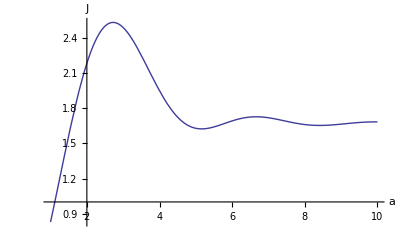

conv_diff_J.pdf

```mathematica
J[a_]=Integrate[u[x,a]^2,{x,0,1}];
Plot[J[a],{a,amin,amax},PlotStyle->Thick,AxesLabel->{a,J}]
Export["conv_diff_J.pdf",%]
```

```mathematica
J[a]
```

(5 (a (45+2 a^4)+45 a Cos[2 a]+15 (-3+a^2) Sin[2 a]))/(6 a^5)

```mathematica
mean=Integrate[J[a],{a,amin,amax}]
N[mean,20]
```

(87960+20000 Cos[2]-20 Cos[20]-30000 Sin[2]+3 Sin[20])/3200

16.360224268375817638